```mathematica
vbar=287.8(*km/sec*);
vtilde=247(*km/sec*);
```

```mathematica
fMB[v_]:=(3/(2π vbar^2))^(3/2)4π v^2 Exp[-(3 v^2)/(2 vbar^2)]
```

```mathematica
ηnum=√(3/(2 vbar^2))vtilde;
```

```mathematica
fMBboosted[x_,η_]:=√(3/(2 vbar^2))4/(√π)x^2 Exp[-x^2]Exp[-η^2] Sinh[2 x η]/(2x η)
```

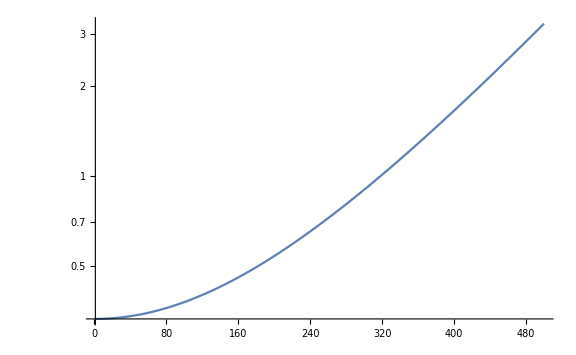

```mathematica
LogPlot[fMBboosted[√(3/(2 vbar^2))v,ηnum]/fMB[v],{v,1,500},PlotRange->Full,ImageSize->Large]
```